## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"drag.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"AVS.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
boatboatboat[boat_]:=Quiet@Module[{doesFloat,doesFloatFlat, trimAngle,stabilityPlot,stabilityAngles},
doesFloat=Volume[region/.boat]Quantity[, ("Centimeters")^3]*Quantity[1, ("Grams")/("Centimeters")^3]>totalMass[boat]Quantity[, "Grams"];
doesFloatFlat=rightingArm[boat,{0,1,0},N@10 Degree]>0&&rightingArm[boat,{0,1,0},N@-10 Degree]<0;
trimAngle=Round[avs[boat,{1,0,0},0]*180/Pi] HoldForm[Degree];
stabilityPlot=Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi,Pi},PlotPoints->6, MaxRecursion->2];
stabilityAngles=DeleteDuplicates@Round[Table[avs[boat,{0,1,0},i],{i,-Pi,Pi,Pi/3}]*180/Pi] HoldForm[Degree];

Grid[{{Style[name/.boat,FontSize->60,FontFamily->"Purisa"],SpanFromLeft},
{showBoat[boat,{0,0,1}],SpanFromLeft},
{"Is it a boat?","Boatboat."},
{"Does it float?",doesFloat},
{"Stability curve",stabilityPlot},
{"Does it float flat?",doesFloatFlat},
{"Trim Angle?",trimAngle},
{"What's the AVS?",stabilityAngles}
},Frame->All]
]
```

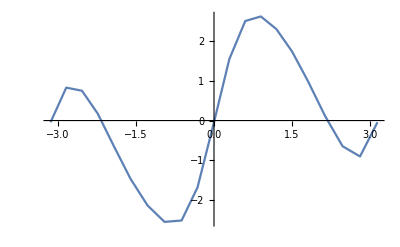
Crapboat | 
-Graphics3D- | 
Is it a boat? | Boatboat.
Does it float? | True
Stability curve | -Graphics-
Does it float flat? | True
Trim Angle? | -49 °
What's the AVS? | {-180 °,-124 °,°,125 °,180 °}

```mathematica
boatboatboat[boat]
```